# Комиссаров А.Е. лаб6,7

## ЛАБОРАТОРНАЯ 6 : Элементарная описательная статистика

{307/4,149/2,(√(10023/19))/2,{62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96}}

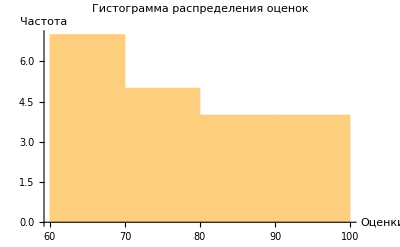

```mathematica
grades=RandomInteger[{60,100},20];(*Создаем случайный набор данных оценок*)
(*Вычисляем среднее значение,медиану,стандартное отклонение и диапазон*)mean=Mean[grades];
median=Median[grades];
stdDev=StandardDeviation[grades];
range=Range[Min[grades],Max[grades]];

(*Выводим результаты*)
{mean,median,stdDev,range}
(*Строим гистограмму распределения оценок*)Histogram[grades,{10},AxesLabel->{"Оценки","Частота"},PlotLabel->"Гистограмма распределения оценок"]
```

## Работа со статическими распределениями

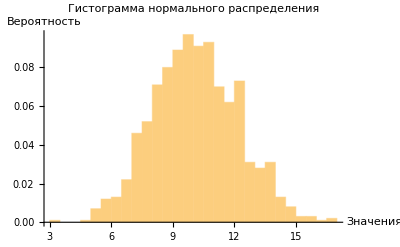

Epilog→{Text[Mean,{10.1119,0.02}],Text[Median,{10.0331,0.02}],RGBColor[1, 0, 0],Line[{{10.1119,0},{10.1119,0.15}}],RGBColor[0, 1, 0],Line[{{10.0331,0},{10.0331,0.15}}]}

{10.1119,2.06871,{8.65802,10.0331,11.5318}}

```mathematica
(*Генерируем выборку из нормального распределения*)data=RandomVariate[NormalDistribution[10,2],1000];
(*Вычисляем среднее значение,стандартное отклонение и квантили*)mean=Mean[data];
stdDev=StandardDeviation[data];
quantiles=Quantile[data,{0.25,0.5,0.75}]; (*значение,которое заданная случайная величина не превышает с фиксированной вероятностью*)

(*Строим гистограмму распределения*)
Histogram[data,Automatic,"Probability",AxesLabel->{"Значения","Вероятность"},PlotLabel->"Гистограмма нормального распределения"]

(*Добавляем линию среднего значения и медианы на гистограмму*)
Epilog->{Text["Mean",{mean,0.02}],Text["Median",{quantiles[[2]],0.02}],Red,Line[{{mean,0},{mean,0.15}}],Green,Line[{{quantiles[[2]],0},{quantiles[[2]],0.15}}]}

(*Выводим результаты*)
{mean,stdDev,quantiles}
```

## Проверка гипотез о математическом ожидании

IndependentUnitTTest[{{9.01877,13.3479,10.4417,5.35323,12.2048,9.347,12.8482,12.6542,8.69914,9.14775,8.48909,8.44749,7.95681,12.5938,12.3268,6.79057,10.3643,11.2354,12.0372,11.6961,9.7445,3.69756,7.80262,11.7316,9.64727,10.9829,8.22958,10.4982,9.56894,8.55245,10.4053,8.47812,9.3056,4.28564,6.74052,12.7396,10.0146,10.7418,10.4957,9.65553,9.58366,11.3788,11.8461,10.9081,12.5445,11.6099,7.44047,9.388,6.22674,8.79863},{14.7091,13.5952,11.3386,15.2788,9.61418,13.4718,15.5638,10.8702,9.05749,13.0114,12.2092,11.6635,9.99362,11.0806,13.7878,13.7947,9.47732,9.18383,10.8914,10.9261,14.1972,10.1241,7.50907,12.6476,11.3478,14.6728,11.5686,12.6375,10.17,12.406,9.90968,12.2289,9.94017,9.0102,10.6948,13.882,14.0655,11.6259,10.4641,10.647,17.021,12.2667,14.0977,12.335,12.2809,12.5417,12.4126,10.5474,14.4862,12.7496,10.5146,15.0174,8.86827,13.9651,10.9643,10.3461,11.5424,7.6649,13.1825,9.53881}}]

IndependentUnitTTest[{{9.01877,13.3479,10.4417,5.35323,12.2048,9.347,12.8482,12.6542,8.69914,9.14775,8.48909,8.44749,7.95681,12.5938,12.3268,6.79057,10.3643,11.2354,12.0372,11.6961,9.7445,3.69756,7.80262,11.7316,9.64727,10.9829,8.22958,10.4982,9.56894,8.55245,10.4053,8.47812,9.3056,4.28564,6.74052,12.7396,10.0146,10.7418,10.4957,9.65553,9.58366,11.3788,11.8461,10.9081,12.5445,11.6099,7.44047,9.388,6.22674,8.79863},{14.7091,13.5952,11.3386,15.2788,9.61418,13.4718,15.5638,10.8702,9.05749,13.0114,12.2092,11.6635,9.99362,11.0806,13.7878,13.7947,9.47732,9.18383,10.8914,10.9261,14.1972,10.1241,7.50907,12.6476,11.3478,14.6728,11.5686,12.6375,10.17,12.406,9.90968,12.2289,9.94017,9.0102,10.6948,13.882,14.0655,11.6259,10.4641,10.647,17.021,12.2667,14.0977,12.335,12.2809,12.5417,12.4126,10.5474,14.4862,12.7496,10.5146,15.0174,8.86827,13.9651,10.9643,10.3461,11.5424,7.6649,13.1825,9.53881}}][TestConclusion]

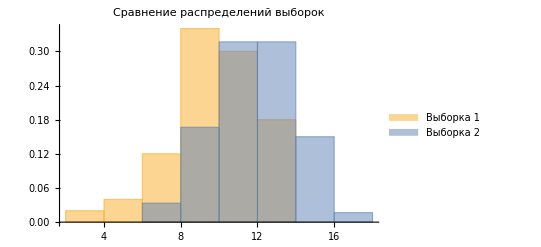

```mathematica
(*Создаем две выборки данных*)sample1=RandomVariate[NormalDistribution[10,2],50];
sample2=RandomVariate[NormalDistribution[12,2],60];
(*Выполняем t-тест*)tTestResult=IndependentUnitTTest[{sample1,sample2}]

(*Выводим результаты*)
tTestResult["TestConclusion"]
(*Строим гистограммы двух выборок*)Histogram[{sample1,sample2},Automatic,"Probability",PlotLabel->"Сравнение распределений выборок",ChartLegends->{"Выборка 1","Выборка 2"}]
```

## Работа со столбцами данных

ID | Value1 | Value2
1 | 2 | 0.953215
2 | 3 | 0.222029
3 | 5 | 0.938459
4 | 3 | 0.79849
5 | 4 | 0.688745
6 | 4 | 0.060062
7 | 2 | 0.389511
8 | 5 | 0.72881
9 | 8 | 0.863762
10 | 7 | 0.225708

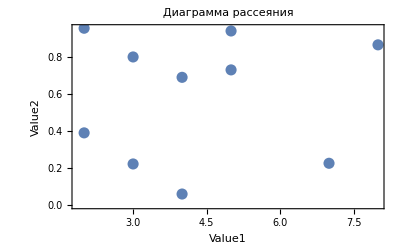

```mathematica
(*Создаем новую таблицу данных*)data2=Table[{i,RandomInteger[{1,10}],RandomReal[{0,1}]},{i,1,10}];

(*Выводим таблицу данных*)
TableForm[data2,TableHeadings->{None,{"ID","Value1","Value2"}}]
(*Строим диаграмму рассеяния*)ListPlot[data2[[All,{2,3}]],PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{"Value1","Value2"},PlotLabel->"Диаграмма рассеяния"]
```

## Выполнение операций с подгруппами данных

```mathematica
(*Создаем таблицу данных с группами*)dataWithGroups=Table[{RandomChoice[{"GroupA","GroupB"}],RandomInteger[{1,10}],RandomReal[{0,1}]},{i,1,20}];

(*Выводим таблицу данных*)
TableForm[dataWithGroups,TableHeadings->{None,{"Group","Value1","Value2"}}]
(*Группируем данные по значениям в столбце "Group"*)groupedData=GroupBy[dataWithGroups,First]

(*Выводим результаты группировки*)
KeyValueMap[Print[#1,": ",#2]&,groupedData]
(*Вычисляем среднее значение для каждой группы*)meanValues=Mean/@groupedData

(*Выводим результаты*)
TableForm[{Keys[groupedData],meanValues},TableHeadings->{{"Group","MeanValue1","MeanValue2"},None}]
(*Выполняем другие операции с подгруппами,например,вычисление суммы значений в каждой группе*)totalValues=Total/@groupedData

(*Выводим результаты*)
TableForm[{Keys[groupedData],totalValues},TableHeadings->{{"Group","TotalValue1","TotalValue2"},None}]
```

Group | Value1 | Value2
GroupB | 1 | 0.144012
GroupB | 7 | 0.542297
GroupB | 8 | 0.22825
GroupA | 7 | 0.222023
GroupA | 5 | 0.61374
GroupA | 10 | 0.32948
GroupB | 5 | 0.171888
GroupB | 1 | 0.506704
GroupB | 3 | 0.684916
GroupB | 7 | 0.275624
GroupB | 7 | 0.802874
GroupB | 1 | 0.317656
GroupB | 7 | 0.302471
GroupB | 8 | 0.456616
GroupA | 8 | 0.253886
GroupB | 9 | 0.36584
GroupB | 1 | 0.221196
GroupB | 6 | 0.186993
GroupB | 9 | 0.5225
GroupA | 8 | 0.491279

<|GroupB→{{GroupB,1,0.144012},{GroupB,7,0.542297},{GroupB,8,0.22825},{GroupB,5,0.171888},{GroupB,1,0.506704},{GroupB,3,0.684916},{GroupB,7,0.275624},{GroupB,7,0.802874},{GroupB,1,0.317656},{GroupB,7,0.302471},{GroupB,8,0.456616},{GroupB,9,0.36584},{GroupB,1,0.221196},{GroupB,6,0.186993},{GroupB,9,0.5225}},GroupA→{{GroupA,7,0.222023},{GroupA,5,0.61374},{GroupA,10,0.32948},{GroupA,8,0.253886},{GroupA,8,0.491279}}|>

GroupB: {{GroupB,1,0.144012},{GroupB,7,0.542297},{GroupB,8,0.22825},{GroupB,5,0.171888},{GroupB,1,0.506704},{GroupB,3,0.684916},{GroupB,7,0.275624},{GroupB,7,0.802874},{GroupB,1,0.317656},{GroupB,7,0.302471},{GroupB,8,0.456616},{GroupB,9,0.36584},{GroupB,1,0.221196},{GroupB,6,0.186993},{GroupB,9,0.5225}}

GroupA: {{GroupA,7,0.222023},{GroupA,5,0.61374},{GroupA,10,0.32948},{GroupA,8,0.253886},{GroupA,8,0.491279}}

{Null,Null}

<|GroupB→{GroupB,16/3,0.381989},GroupA→{GroupA,38/5,0.382082}|>

Group | GroupB | GroupA
MeanValue1 | <|GroupB→{GroupB,16/3,0.381989},GroupA→{GroupA,38/5,0.382082}|> | 
MeanValue2 |  |

<|GroupB→{15 GroupB,80,5.72984},GroupA→{5 GroupA,38,1.91041}|>

Group | GroupB | GroupA
TotalValue1 | <|GroupB→{15 GroupB,80,5.72984},GroupA→{5 GroupA,38,1.91041}|> | 
TotalValue2 |  |

## Замена или удаление недостающих или недействительных данных

```mathematica
(*Создаем таблицу данных с недостающими значениями*)dataWithMissingValues=Table[{RandomInteger[{1,5}],RandomChoice[{1,2,Missing[]}],RandomReal[{0,1}]},{i,1,20}];

(*Выводим таблицу данных*)
TableForm[dataWithMissingValues,TableHeadings->{None,{"ID","Value","Value2"}}]

(*Заменяем недостающие значения в столбце "Value" на-1*)
dataWithMissingValues=Replace[dataWithMissingValues,{a_,Missing[],b_}:>{a,-1,b},{1}];

(*Выводим обновленную таблицу данных*)
TableForm[dataWithMissingValues,TableHeadings->{None,{"ID","Value","Value2"}}]
```

ID | Value | Value2
3 | 2 | 0.478883
3 | 2 | 0.714254
1 | 2 | 0.0503786
1 | Missing[] | 0.947984
5 | 1 | 0.180082
3 | Missing[] | 0.624372
5 | Missing[] | 0.924
5 | 1 | 0.247791
3 | 2 | 0.00506866
4 | Missing[] | 0.396061
5 | 1 | 0.527367
3 | Missing[] | 0.696709
4 | Missing[] | 0.213484
4 | 2 | 0.29241
1 | Missing[] | 0.611722
1 | 2 | 0.278453
2 | Missing[] | 0.0514306
5 | Missing[] | 0.450731
1 | Missing[] | 0.405635
1 | 2 | 0.710776

ID | Value | Value2
3 | 2 | 0.478883
3 | 2 | 0.714254
1 | 2 | 0.0503786
1 | -1 | 0.947984
5 | 1 | 0.180082
3 | -1 | 0.624372
5 | -1 | 0.924
5 | 1 | 0.247791
3 | 2 | 0.00506866
4 | -1 | 0.396061
5 | 1 | 0.527367
3 | -1 | 0.696709
4 | -1 | 0.213484
4 | 2 | 0.29241
1 | -1 | 0.611722
1 | 2 | 0.278453
2 | -1 | 0.0514306
5 | -1 | 0.450731
1 | -1 | 0.405635
1 | 2 | 0.710776

```mathematica
dataWithMissingValues=Table[{RandomInteger[{1,5}],RandomChoice[{1,2,Missing[]}],RandomReal[{0,1}]},{i,1,20}];

(*Выводим таблицу данных*)
TableForm[dataWithMissingValues,TableHeadings->{None,{"ID","Value","Value2"}}]
(*Удаляем строки с недостающими значениями в столбце "Value"*)
dataWithoutMissingValues=DeleteCases[dataWithMissingValues,{_,Missing[],_}];

(*Выводим обновленную таблицу данных*)
TableForm[dataWithoutMissingValues,TableHeadings->{None,{"ID","Value","Value2"}}]
```

ID | Value | Value2
5 | 2 | 0.967243
5 | Missing[] | 0.44862
4 | Missing[] | 0.652114
4 | 2 | 0.238405
5 | 2 | 0.0896248
2 | 2 | 0.287128
5 | 1 | 0.236321
2 | Missing[] | 0.603856
2 | 1 | 0.95731
5 | Missing[] | 0.154707
3 | 1 | 0.729842
2 | 2 | 0.209221
2 | Missing[] | 0.996428
1 | 1 | 0.811127
1 | 1 | 0.347264
2 | 2 | 0.63835
2 | 2 | 0.871763
4 | Missing[] | 0.764121
3 | 1 | 0.591468
5 | 2 | 0.446795

ID | Value | Value2
5 | 2 | 0.967243
4 | 2 | 0.238405
5 | 2 | 0.0896248
2 | 2 | 0.287128
5 | 1 | 0.236321
2 | 1 | 0.95731
3 | 1 | 0.729842
2 | 2 | 0.209221
1 | 1 | 0.811127
1 | 1 | 0.347264
2 | 2 | 0.63835
2 | 2 | 0.871763
3 | 1 | 0.591468
5 | 2 | 0.446795

## Выполнение линейной регрессии

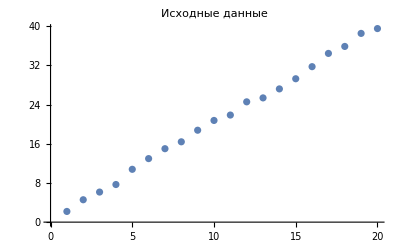

0.602155+1.95924 x

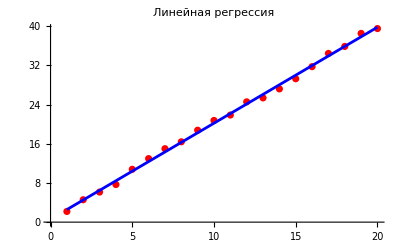

```mathematica
(*Создаем случайные данные для линейной регрессии*)dataForRegression=Table[{i,2*i+RandomReal[{-1,1}]},{i,1,20}];

(*Выводим данные*)
ListPlot[dataForRegression,PlotLabel->"Исходные данные"]
(*Применяем линейную регрессию*)linearModel=LinearModelFit[dataForRegression,x,x];

(*Выводим результаты регрессии*)
linearModel["BestFit"]
(*Строим график исходных данных и регрессионной линии*)Show[ListPlot[dataForRegression,PlotStyle->Red,PlotLabel->"Линейная регрессия"],Plot[linearModel[x],{x,Min[dataForRegression[[All,1]]],Max[dataForRegression[[All,1]]]},PlotStyle->Blue]]
```

## ЛАБОРАТОРНАЯ 7 : Подбор модели с учётом погрешности измерений

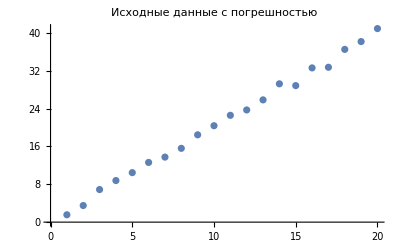

0.2469+1.98033 x

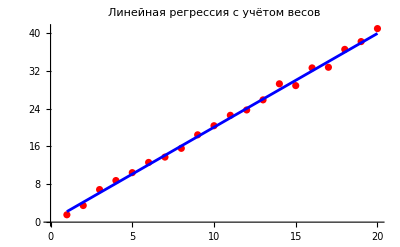

```mathematica
(*Создаем случайные данные с погрешностью*)data=Table[{i,2*i+RandomReal[{-1,1}]},{i,1,20}];

(*Добавляем случайную погрешность к значениям*)
dataWithErrors=Transpose[{data[[All,1]],data[[All,2]]+RandomReal[{-0.5,0.5},Length[data]]}];

(*Выводим данные*)
ListPlot[dataWithErrors,PlotLabel->"Исходные данные с погрешностью"]
(*Применяем линейную регрессию с учётом весов*)weightedLinearModel=LinearModelFit[dataWithErrors,x,x,Weights->1/RandomReal[{0.5,2},Length[dataWithErrors]]];

(*Выводим результаты регрессии*)
weightedLinearModel["BestFit"]
(*Строим график исходных данных и линии регрессии*)Show[ListPlot[dataWithErrors,PlotStyle->Red,PlotLabel->"Линейная регрессия с учётом весов"],Plot[weightedLinearModel[x],{x,Min[dataWithErrors[[All,1]]],Max[dataWithErrors[[All,1]]]},PlotStyle->Blue]]
```

## Диагностика результатов для модели, найденной путём подбора

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.2469 | 0.358061 | 0.689546 | 0.499274
x | 1.98033 | 0.0295562 | 67.0023 | 4.80018×10^-23

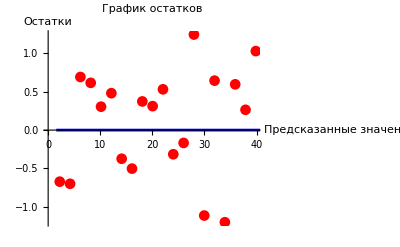

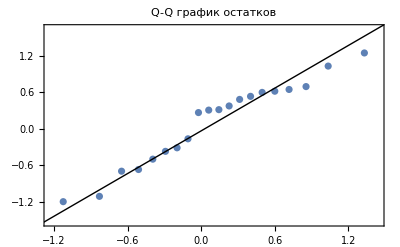

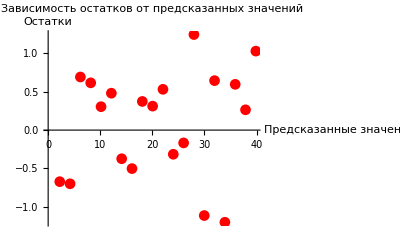

```mathematica
(*Выводим стандартные ошибки коэффициентов*)weightedLinearModel["ParameterTable"]
(*Выводим график остатков*)Show[ListPlot[Transpose[{weightedLinearModel["PredictedResponse"],weightedLinearModel["FitResiduals"]}],PlotLabel->"График остатков",AxesLabel->{"Предсказанные значения","Остатки"},PlotStyle->Red,PlotMarkers->Automatic],Plot[0,{x,Min[dataWithErrors[[All,2]]],Max[dataWithErrors[[All,2]]]},PlotStyle->Blue]]
(*Выводим Q-Q график остатков*)QuantilePlot[weightedLinearModel["FitResiduals"],PlotLabel->"Q-Q график остатков"]
(*Выводим график зависимости остатков от предсказанных значений*)ListPlot[Transpose[{weightedLinearModel["PredictedResponse"],weightedLinearModel["FitResiduals"]}],PlotLabel->"Зависимость остатков от предсказанных значений",AxesLabel->{"Предсказанные значения","Остатки"},PlotStyle->Red,PlotMarkers->Automatic]
```

## Графические инструменты проверки корректности подбора модели по точкам

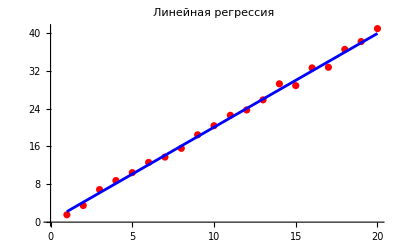

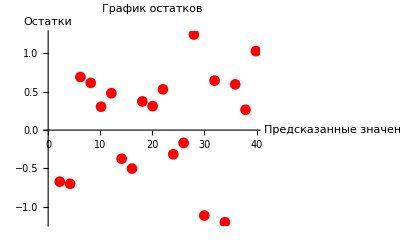

-Graphics-

-Graphics-

```mathematica
(*Строим график исходных данных и регрессионной линии*)Show[ListPlot[dataWithErrors,PlotStyle->Red,PlotLabel->"Линейная регрессия"],Plot[weightedLinearModel[x],{x,Min[dataWithErrors[[All,1]]],Max[dataWithErrors[[All,1]]]},PlotStyle->Blue]]
(*Строим график остатков*)ListPlot[Transpose[{weightedLinearModel["PredictedResponse"],weightedLinearModel["FitResiduals"]}],PlotLabel->"График остатков",AxesLabel->{"Предсказанные значения","Остатки"},PlotStyle->Red,PlotMarkers->Automatic]
(*Строим график зависимости остатков от предсказанных значений*)ListPlot[Transpose[{weightedLinearModel["PredictedResponse"],weightedLinearModel["FitResiduals"]}],PlotLabel->"Зависимость остатков от предсказанных значений",AxesLabel->{"Предсказанные значения","Остатки"},PlotStyle->Red,PlotMarkers->Automatic]
(*Выводим Q-Q график остатков*)QuantilePlot[weightedLinearModel["FitResiduals"],PlotLabel->"Q-Q график остатков"]
```

## Выполнение бутстреп-анализа

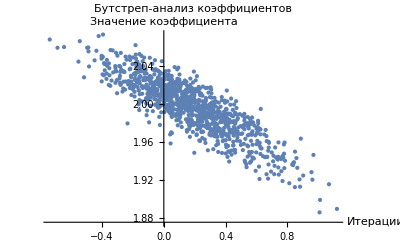

```mathematica
bootstrapIteration[dataWithErrors_]:=Module[{n,bootstrappedData,bootstrapModel},n=Length[dataWithErrors];
(*Создаем бутстреп-выборку с заменой*)bootstrappedData=RandomChoice[dataWithErrors,n];
(*Применяем линейную регрессию к бутстреп-выборке*)bootstrapModel=LinearModelFit[bootstrappedData,x,x];
(*Возвращаем коэффициенты модели*)bootstrapModel["BestFitParameters"]]
(*Задаем количество итераций бутстрепа*)numIterations=1000;

(*Выполняем бутстреп-анализ и собираем коэффициенты*)
bootstrapCoefficients=Table[bootstrapIteration[dataWithErrors],{numIterations}];

(*Выводим результаты*)
ListPlot[bootstrapCoefficients,PlotLabel->"Бутстреп-анализ коэффициентов",AxesLabel->{"Итерации","Значение коэффициента"},PlotStyle->PointSize[Small]]
```

## Моделирование методом Монте-Карло

```mathematica
(*Определяем функцию для проверки,находится ли точка внутри четверти круга*)pointInsideCircleQ[{x_,y_}]:=x^2+y^2<=1

(*Определяем функцию для моделирования методом Монте-Карло*)
monteCarloPiEstimation[n_]:=Module[{pointsInsideCircle,totalPoints},(*Генерируем случайные точки в квадрате[0,1] x[0,1]*)randomPoints=RandomReal[1,{n,2}];
(*Проверяем,сколько точек попало внутрь четверти круга*)pointsInsideCircle=Select[randomPoints,pointInsideCircleQ];
(*Вычисляем оценку числа π*)4.0 Length[pointsInsideCircle]/n]

(*Выполняем моделирование с разными значениями n*)
nValues={100,1000,10000,100000,1000000};
piEstimations=Table[monteCarloPiEstimation[n],{n,nValues}]

(*Выводим результаты*)
TableForm[Transpose[{nValues,piEstimations}],TableHeadings->{None,{"Число точек","Оценка π"}}]
```

{3.04,3.14,3.1272,3.13424,3.14598}

Число точек | Оценка π
100 | 3.04
1000 | 3.14
10000 | 3.1272
100000 | 3.13424
1000000 | 3.14598